| Estimate | Standard Error | t-Statistic | P-Value
a | -14.5364 | 0.850263 | -17.0964 | 0.00340385
b | 52.9262 | 0.14422 | 366.983 | 7.42512×10^-6

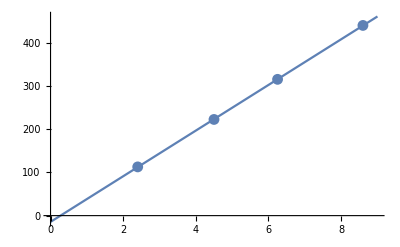

```mathematica
times = {2.4, 4.5, 6.25, 8.6};
channels = {113, 223, 316, 441};
data = Transpose[{times, channels}];
nlm = NonlinearModelFit[data, a + b x, {a, b}, x];
nlm["ParameterTable"]
Show[Plot[Normal[nlm], {x, 0, 9}],ListPlot[data, PlotRange->{{0, 11}, All}, Frame->True]]
```